# Graph Complexity

## Program

```mathematica
scaleEntropy[l_]:=Module[{mean},
mean=Mean[l];
Entropy[l]*mean
]
```

```mathematica
totalEntropy[l_]:=Module[{total},
total=Total[l];
total^Entropy[l]
]
```

```mathematica
fullCompleteGraph[n_,l_]:=AdjacencyGraph[Table[l,{n},{n}],DirectedEdges->True]
```

```mathematica
fullCompleteGraph[3,2]
```

-Graphics-

```mathematica
graphRedundancyComplexity[g_Graph]:=Module[{vc,ec,ecmean,etp},
vc=VertexCount[g]//N;
ec=EdgeCount[g]//N;
ecmean = ec/(vc^2);
etp=Entropy[AdjacencyMatrix[g]//Flatten]//N;
(vc) (vc^ecmean) Exp[etp]
]
```

```mathematica
graphComplexity[g_Graph]:=Module[{vc,ec,etp},
vc=VertexCount[g]//N;
ec=EdgeCount[g]//N;
etp=Entropy[AdjacencyMatrix[g]//Flatten]//N;
vc^2 ec etp
]
```

```mathematica
graphComplexityE[g_Graph]:=Module[{vc,ec,etp},
vc=VertexCount[g]//N;
ec=EdgeCount[g]//N;
(*etp=Entropy[AdjacencyMatrix[g]//Flatten]//N;*)
etp=Entropy[Map[#[[2]]&,Tally[EdgeList[g]]]]//N;
vc^2 ec etp
]
```

```mathematica
graphComplexityD[g_Graph]:=Module[{ec,etp,vc,vinetp,voutetp},
ec=EdgeCount[g]//N;
vc=VertexCount[g]//N;
etp=Entropy[AdjacencyMatrix[g]//Flatten]//N;
vinetp=Entropy[VertexInDegree[g]]//N;
voutetp=Entropy[VertexOutDegree[g]]//N;
ec etp vc vinetp vc voutetp
]
```

```mathematica
graphComplexityDp[g_Graph]:=Module[{ec,etp,vc,vinetp,voutetp},
ec=EdgeCount[g]//N;
vc=VertexCount[g]//N;
etp=Entropy[AdjacencyMatrix[g]//Flatten]//N;
vinetp=Entropy[VertexInDegree[g]]//N;
voutetp=Entropy[VertexOutDegree[g]]//N;
ec^etp vc^vinetp vc^voutetp
]
```

## Test

### Graph

```mathematica
gv0=Graph[{1,2,3},{}]
```

-Graphics-

```mathematica
gv1=AdjacencyGraph[ Table[1,{n,3},{n,3}] ,DirectedEdges->True]
```

-Graphics-

```mathematica
gv2=AdjacencyGraph[ Table[2,{n,3},{n,3}] ,DirectedEdges->True]
```

-Graphics-

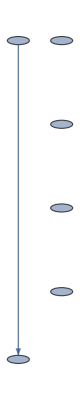

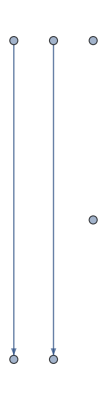

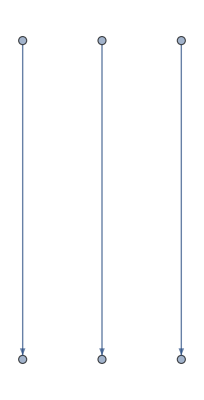

```mathematica
ge1=Graph[{1,2,3,4,5,6},{1->2}]
ge2=Graph[{1,2,3,4,5,6},{1->2,3->4}]
ge3=Graph[{1,2,3,4,5,6},{1->2,3->4,5->6}]
```

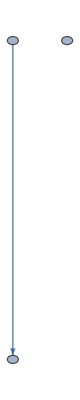

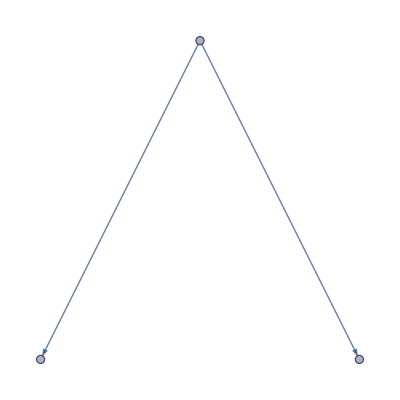

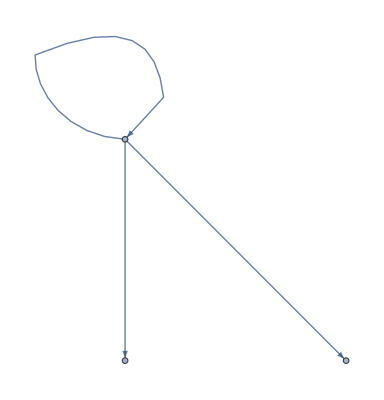

```mathematica
g11=Graph[{1,2,3},{1->2}]
g12=Graph[{1,2,3},{1->2,1->3}]
g13=Graph[{1,2,3},{1->2,1->3,1->1}]
```

```mathematica
cg1=CompleteGraph[4,DirectedEdges->True]
```

-Graphics-

```mathematica
fcg1=fullCompleteGraph[4,1]
```

-Graphics-

```mathematica
(gr1=CompleteGraph[6,DirectedEdges->True])//EdgeCount
```

30

```mathematica
gr2=Graph[Range[6],Table[RandomInteger[1,6]->RandomInteger[1,6],{30}]]
```

-Graphics-

```mathematica
(gr11=fullCompleteGraph[6,1])//EdgeCount
```

36

```mathematica
gr12=Graph[Range[6],Table[RandomInteger[1,6]->RandomInteger[1,6],{36}]]
```

-Graphics-

### Test of graphRedundancyComplexity

```mathematica
graphRedundancyComplexity[gv0]
graphRedundancyComplexity[gv1]
graphRedundancyComplexity[gv2]
```

3.

9.

27.

```mathematica
graphRedundancyComplexity[ge1]
graphRedundancyComplexity[ge2]
graphRedundancyComplexity[ge3]
```

7.15965

8.21417

9.28044

```mathematica
graphRedundancyComplexity[g11]
graphRedundancyComplexity[g12]
graphRedundancyComplexity[g13]
```

4.80431

6.50424

8.17704

```mathematica
graphRedundancyComplexity[cg1]
graphRedundancyComplexity[fcg1]
```

19.8529

16.

```mathematica
graphRedundancyComplexity[gr1]
graphRedundancyComplexity[gr2]
```

41.907

49.6654

```mathematica
graphRedundancyComplexity[gr11]
graphRedundancyComplexity[gr12]
```

36.

57.0447

### Compare

entropy

```mathematica
scaleEntropy[{0,0,0,1}]//N
scaleEntropy[{1,1,0,1}]//N
scaleEntropy[{0,0,0,1,0}]//N
```

0.140584

0.421751

0.10008

```mathematica
totalEntropy[{0,0,0,1}]//N
totalEntropy[{1,1,0,1}]//N
totalEntropy[{0,0,0,1,0}]//N
```

1.

1.85482

1.

## Memo